Příklad Ia - 1)

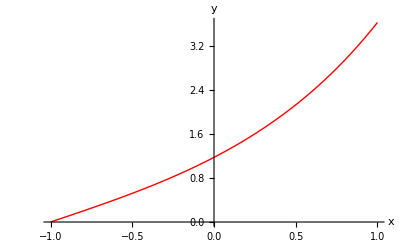

```mathematica
ClearAll["Global`*"]
f[x_] := Sinh[x^2]
Plot[f[Sqrt[t + 1]], {t, -1, 1}, AxesLabel -> {"x", "y"}, PlotStyle -> {Thick, Red}]
```

Příklad Ia - 2)

```mathematica
ClearAll["Global`*"]
rovnice1 = b + 2*c + a == 3;
rovnice2 = 5*a - 3*b + 2*c == -4;
rovnice3 = -21*a + 15*c == 3;

solution = Solve[{rovnice1, rovnice2, rovnice3}][[1]]
vyr = Sqrt[a] + b^2+c^2 + 0.0 /. solution
N[vyr] (* vyčíslí hodnotu, N[x, n] na počet desetinných míst *)
```

{a→17/96,b→185/96,c→43/96}

4.33509

4.33509

Příklad 1a - 3)

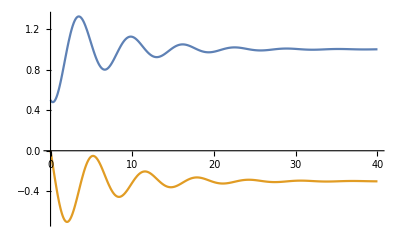

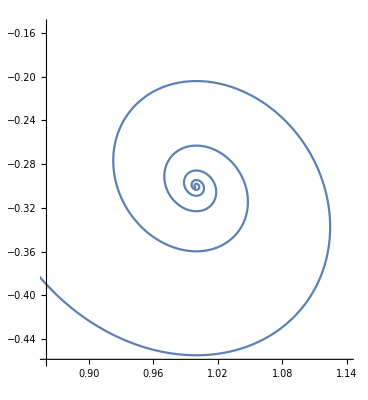

```mathematica
ClearAll["Global`*"]
reseni = DSolve[{x1'[t]+x2[t]==-3/10*x1[t],x1[t]-x2'[t]==1,x1[0]==1/2,x2[0]==0}, {x1, x2}, t][[1]];
rovniceX1 = x1 /. reseni[[1]];
rovniceX2 = x2 /. reseni[[2]];

Plot[{rovniceX1[t], rovniceX2[t]}, {t, 0, 40}]
ParametricPlot[{ rovniceX1[t], rovniceX2[t]}, {t, 0, 40}]
```